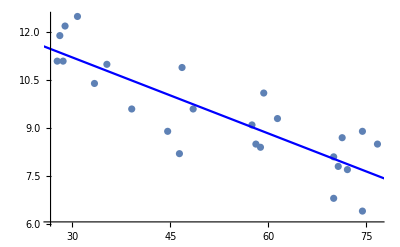

```mathematica
data={{35.3,27.7,30.8,58.8,61.4,71.3,74.4,76.7,70.7,57.5,46.4,28.9,28.1,39.1,46.8,48.5,59.3,70,70,74.4,72.1,58.1,44.6,33.4,28.6},{11,11.1,12.5,8.4,9.3,8.7,6.4,8.5,7.8,9.1,8.2,12.2,11.9,9.6,10.9,9.6,10.1,8.1,6.8,8.9,7.7,8.5,8.9,10.4,11.1}};
n=Length[data[[1]]];
xi=Sum[data[[1,i]],{i,1,n}];
yi=Sum[data[[2,i]],{i,1,n}];
x2=Sum[data[[1,i]]^2,{i,1,n}];
y2=Sum[data[[2,i]]^2,{i,1,n}];
xy=Sum[data[[1,i]]*data[[2,i]],{i,1,n}];
Sxx = Sum[(data[[1, i]]-Total[data[[1]]]/n)^2, {i, 1,n}];
Sxy = Sum[(data[[1, i]]-Total[data[[1]]]/n)*(data[[2, i]]-Total[data[[2]]]/n), {i, 1,n}];
Syy =  Sum[(data[[2, i]]-Total[data[[2]]]/n)^2, {i, 1,n}];
SSE = Sum[(data[[2,i]]-(b0+b1*data[[1,i]]))^2, {i,1,n}];
s2 = N[SSE/(n-2)];
b1 = Sxy/Sxx;
b0 = Total[data[[2]]]/n-b1*Total[data[[1]]]/n;
Show[ListPlot[Transpose[data]], Plot[b0+b1*x,{x,0,100}, PlotStyle->Blue]]
```